# PHAS2443: Practical Mathematics II Exercises 1: Programming Styles

This set of exercises starts with a few simple revision problems, before setting up a module for an alternative method of finding the zero of a function (Newton's method was discussed in the lecture). Remember how useful the help file can be.

1. Given a list, {a,b,c,d,e,f,g,h,i,j,k}, form a new list containing just the elements in the even-numbered positions (2,4,6,...). Do this in three ways:
                  a) with a Do loop and AppendTo
                  b) with a Table command
                  c) using Partition and taking part of the transpose of the result.
       By enclosing your schemes in a Do loop and repeating them 100000 times, compare the timings.

```mathematica
list = {a,b,c,d,e,f,g,h,i,j,k};
```

```mathematica
DoList = {};
Do[AppendTo[DoList, list[[n]]], {n, 2, Length[list], 2}]
DoList
```

{b,d,f,h,j}

```mathematica
TableList = Table[list[[i]], {i, 2, Length[list], 2}]
```

{b,d,f,h,j}

```mathematica
PartitionList = Transpose[Partition[list, 2]][[2]]
```

{b,d,f,h,j}

```mathematica
DoList = {};
TableList = {};
PartitionList = {};

Timing[Do[Do[AppendTo[DoList, list[[n]]], {n, 2, Length[list], 2}], 10000]]
Timing[Do[Table[list[[i]], {i, 2, Length[list], 2}], 10000]]
Timing[Do[Transpose[Partition[list, 2]][[2]], 10000]]
```

{9.51563,Null}

{0.046875,Null}

{0.0625,Null}

2. Create a function abwordq that accepts as an argument a string containing a word, and returns True if the letters in the word are in alphabetical order, False if they are not. Thus abwordq["how"] will return True, but abwordq["why"] will return False.

Then use the following code to read in a dictionary:
wordfile=DictionaryLookup[x__];
and find the words in that dictionary that have their letters in alphabetical order.

  Repeat, this time looking for palindromes (words that read the same forwards as backwards).

```mathematica
abwordq[x_ ] := 
Module[{order = Ordering[LetterNumber /@ Characters[x]]},
If[
Characters[x][[order]] == Characters[x],
True, False]
]
```

```mathematica
abwordq["how"]
abwordq["why"]
```

True

False

Checking the wordfile for alphabetical words

```mathematica
wordfile=DictionaryLookup[x__];
```

```mathematica
listAbwordqer[x__] := 
Module[ {tempList = {}},
Do[
If[
abwordq[x[[n]]] ,
AppendTo[tempList, x[[n]]]
], 
{n, 1, Length[x]}
];
Print["List of words with alphabetical letters: "];
Print[tempList]
]
```

```mathematica
listAbwordqer[wordfile]
```

### Checking for palindromes

```mathematica
listPalindromer[x__] := 
Module[ {tempList = {}},
Do[
If[
PalindromeQ[x[[n]]],
AppendTo[tempList, x[[n]]]
],
{n, 1, Length[x]}
];
Print["List of palindromes from input: "];
Print[tempList]
]
```

```mathematica
listPalindromer[wordfile]
```

List of palindromes from input

{a,aha,aka,bib,bob,boob,bub,CFC,civic,dad,deed,deified,did,dud,DVD,eke,ere,eve,ewe,eye,gag,gig,huh,I,kayak,kook,level,ma'am,madam,mam,MGM,minim,mom,mum,nan,non,noon,nun,oho,pap,peep,pep,pip,poop,pop,pup,radar,redder,refer,repaper,reviver,rotor,sagas,sees,seres,sexes,shahs,sis,solos,SOS,stats,stets,tat,tenet,TNT,toot,tot,tut,wow,WWW}

3. Convert the following function to one that does not have conditional parts (/;), but uses pattern matching in the argument list instead.
        f[x_,y_]:=x-y/;IntegerQ[x]
    f[x_,y_]:=x[[1]]+y/;Head[x]==List&&IntegerQ[First[x]].

```mathematica
f[x_Integer, y_] := x - y
f[x_List, y_] := x[[1]] + y

f[2,1]
f[{2,1}, 1]
```

1

3

4. The secant method is a method for finding the zero of a function without using derivatives. It starts with two x values, x0 and x1, say, evaluates the value of the function at those points, draws a straight line through the points and finds where it intersects the axis, x2, and then repeats starting with x1 and x2.
  Here is an illustration of the first step of the method.

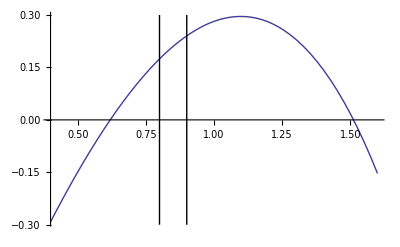

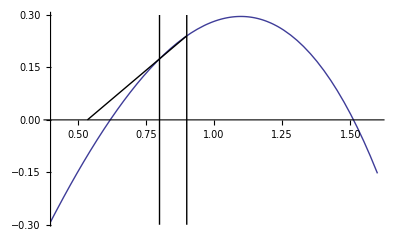

```mathematica
fn:=3 x-ⅇ^x;
p1=Plot[fn,{x,0.4,1.6}];
x0=x->0.8;x1=x->0.9;
l1=Graphics[Line[{{x,-0.3},{x,0.3}}/.x0]];
l2=Graphics[Line[{{x,-0.3},{x,0.3}}/.x1]];
l3=Graphics[Line[{{x,fn}/.x1,{(x/.x0)-((fn/.x0) ((x/.x1)-(x/.x0)))/((fn/.x1)-(fn/.x0)),0}}]];
Show[p1,l1,l2]
Show[p1,l1,l2,l3]
```

Write a module to implement the secant method, using a procedural approach. Your function should return the sequence of x values used.
  Modify your function to use a functional approach.
  Check each version by looking for the roots of 3x - Exp[x].

```mathematica
procSecanter[f_] := 
Module[
{{x0  = 0}, {x1 = 1}, {x2 = 1}, {m = (y2 - y1) / (x2- x1)} 
{
line[x_] :=   m x + (y1 - m x1) 
},
While[
f[x2] ≠ 0,

y0 = f[x0]; y1 = f[x1];



]
```

A.H. Harker
Physics and Astronomy, UCL
January 2008, revised January 2009.